# Answer to the Question 1

## Part (a)

using Do loop

```mathematica
fact=1;
Do[fact=fact*i,{i,1,11}]
Print["factorial of 11 is ", fact]
```

factorial of 11 is 39916800

Using for loop

```mathematica
For[fact=1;i=1,i≤11,i++,fact=fact*i]
Print["factorial of 11 is ", fact]
```

factorial of 11 is 39916800

Using while loop

```mathematica
fact=1;
i=1;
While[i≤11,fact=fact*i;i++]
Print["factorial of 11 is ", fact]
```

factorial of 11 is 39916800

## Part(b)

Section (i)

```mathematica
s=Sum[1/n,{n,1,21,2}];
Print["Sum of the series is ",s]
```

Sum of the series is 31730711/14549535

Section (ii)

```mathematica
s=Sum[n,{n,1,105,4}];
Print["Sum of the series is ",s]
```

Sum of the series is 1431

## Part (c)

```mathematica
A={1,2,3,4,5,7};
B={1,3,5,7,8};
```

A-B

```mathematica
Complement[A,B]
```

{2,4}

B-A

```mathematica
Complement[B,A]
```

{8}

# Answer to the Question 2

## Part (a)

```mathematica
set={};
Do[If[PrimeQ[i],set=Append[set,i]],{i,1,1300}]
Print["the required numbers are"]
Do[Print[set[[i]],", ",set[[i+1]],", ",set[[i+2]],", ",set[[i+3]],", ",set[[i+4]],", ",set[[i+5]]],{i,1,Length[set],6}]
```

the required numbers are

2, 3, 5, 7, 11, 13

17, 19, 23, 29, 31, 37

41, 43, 47, 53, 59, 61

67, 71, 73, 79, 83, 89

97, 101, 103, 107, 109, 113

127, 131, 137, 139, 149, 151

157, 163, 167, 173, 179, 181

191, 193, 197, 199, 211, 223

227, 229, 233, 239, 241, 251

257, 263, 269, 271, 277, 281

283, 293, 307, 311, 313, 317

331, 337, 347, 349, 353, 359

367, 373, 379, 383, 389, 397

401, 409, 419, 421, 431, 433

439, 443, 449, 457, 461, 463

467, 479, 487, 491, 499, 503

509, 521, 523, 541, 547, 557

563, 569, 571, 577, 587, 593

599, 601, 607, 613, 617, 619

631, 641, 643, 647, 653, 659

661, 673, 677, 683, 691, 701

709, 719, 727, 733, 739, 743

751, 757, 761, 769, 773, 787

797, 809, 811, 821, 823, 827

829, 839, 853, 857, 859, 863

877, 881, 883, 887, 907, 911

919, 929, 937, 941, 947, 953

967, 971, 977, 983, 991, 997

1009, 1013, 1019, 1021, 1031, 1033

1039, 1049, 1051, 1061, 1063, 1069

1087, 1091, 1093, 1097, 1103, 1109

1117, 1123, 1129, 1151, 1153, 1163

1171, 1181, 1187, 1193, 1201, 1213

1217, 1223, 1229, 1231, 1237, 1249

1259, 1277, 1279, 1283, 1289, 1291

## Part (b)

Section (i)

```mathematica
LogicalExpand[p∧(q∨r)]==LogicalExpand[(p∧q)∨(p∧r)]
```

True

Section (ii)

```mathematica
LogicalExpand[¬(p∧q)]==LogicalExpand[¬p∨¬q]
```

True

## Part (c)

```mathematica
For[i=1;k=0,Fibonacci[i]≤1000,i++,k=i]
Print[k," terms of Fibonacci series is less than 1000"]
```

16 terms of Fibonacci series is less than 1000

# Answer to the Question 3

## Part (a)

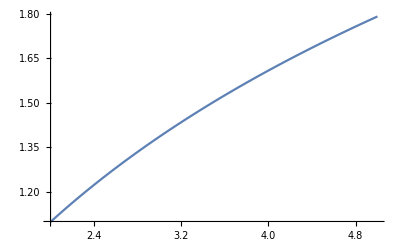

```mathematica
F[x_]:=(1+x^3)/(1+x^2)/;x<1
F[x_]:=Cos[x]/;1≤x≤2
F[x_]:=Log[x+1]/;x>2
Plot[F[x],{x,2,5}]
```

## Part (b)

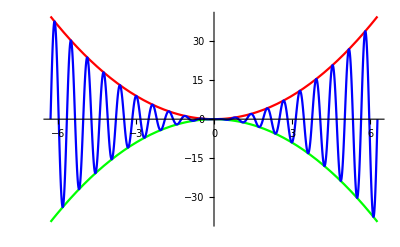

```mathematica
Plot[{x^2,-x^2,x^2*Sin[10*x]},{x,-2*π,2*π},PlotStyle->{Red,Green,Blue}]
```

## Part (c)

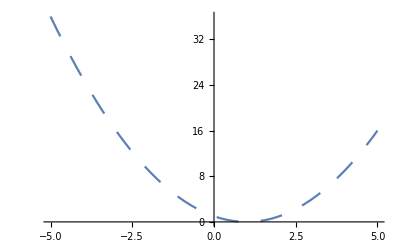

```mathematica
Plot[(x-1)^2,{x,-5,5},PlotStyle->Dashing[0.04]]
```

# Answer to the Question 4

## Part (i)

```mathematica
A=({{2, 2, 1}, {1, 3, 1}, {1, 2, 2}});
CharacteristicPolynomial[A,x]
```

5-11 x+7 x^2-x^3

```mathematica
5*IdentityMatrix[Length[A]]-11*A+7*MatrixPower[A,2]-MatrixPower[A,3]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*hence, the theorem is varified*)
```

## Part (b)

Eigen Value

```mathematica
Eigenvalues[A]
```

{5,1,1}

Eigen Vector

```mathematica
Eigenvectors[A]
```

{{1,1,1},{-1,0,1},{-2,1,0}}

Rank

```mathematica
MatrixRank[A]
```

3

## Part (c)

```mathematica
Inverse[A]//MatrixForm
```

(4/5 | -2/5 | -1/5
-1/5 | 3/5 | -1/5
-1/5 | -2/5 | 4/5)

# Answer to the Question 5

## Part (a)

```mathematica
Clear[a,c]
a={1,2,-3};
b={2,-5,1};
c={3,1,2};
v=Abs[Dot[a,Cross[b,c]]];
Print["The volume is ",v," units"]
```

The volume is 64 units

## Part (b)

```mathematica
x1=1;y1=2;z1=3;
l1=2;m1=-3;n1=4;
x2=2;y2=3;z2=5;
l2=3;m2=4;n2=5;
ang=ArcSin[Sqrt[(m1*n2-n1*m2)^2+(n1*l2-l1*n2)^2+(l1*m2-m1*l2)^2]];
l=(m1*n2-n1*m2)/Sin[ang];
m=(n1*l2-n2*l1)/Sin[ang];
n=(l1*m2-m1*l2)/Sin[ang];
SD=l*(x2-x1)+m*(y2-y1)+n*(z2-z1)//Simplify
A1=({{x-x1, y-y1, z-z1}, {l1, m1, n1}, {l, m, n}});
SD1=Det[A1]//Simplify;
A2=({{x-x1, y-y1, z-z1}, {l2, m2, n2}, {l, m, n}});
SD2=Det[A2]//Simplify;
SD1==0
SD2==0
```

5/(√1254)

-(-642+59 x+158 y+89 z)/(√1254)==0

√(2/627) (-18+29 x-103 y+65 z)==0

# Answer to the Question 6

## Part (a)

```mathematica
x=Cos[4*t];
y=4*Sin[t];
z=6*t;
Sqrt[(D[x,t])^2+(D[y,t])^2+(D[z,t])^2]/.t->{0,π/2}//N
Sqrt[(D[x,{t,2}])^2+(D[y,{t,2}])^2+(D[z,{t,2}])^2]/.t->{0,π/2}//N
```

{7.2111,6.}

{16.,16.4924}

## Part (b)

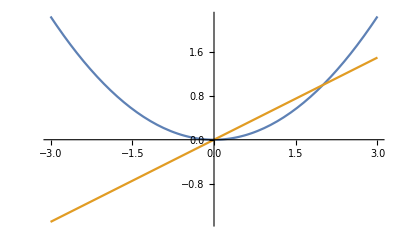

{{y→0},{y→2}}

```mathematica
Clear[F,G,x,y]
F=y^2/4;
G=y/2;
Plot[{F,G},{y,-3,3}]
i=Solve[F==G]
```

```mathematica
a=i[[1,1,2]];
b=i[[2,1,2]];
area=Integrate[G-F,{y,a,b}]//N;
Print["the area is ",area," square units"]
```

the area is 0.333333 square units